```mathematica
f[x_]:=x^4-10x^3+27x^2-2x-40
y=Solve[f[x]==0,x]
```

{{x→-1},{x→2},{x→4},{x→5}}

```mathematica
y[[1]][[1]]
```

x→-1

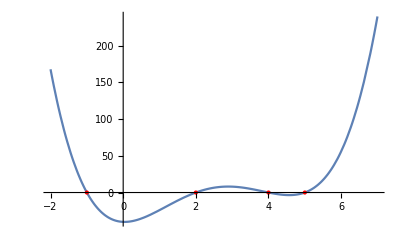

```mathematica
h=Plot[f[x],{x,-2,7},MeshFunctions->{f[x]/.x->#&},Mesh->{{0}},MeshStyle->{PointSize[Large],Red}]
```

```mathematica
f[x0_, y0_, x1_, y1_, x2_, y2_] := Module[{a, b, c, h}, m := a*x^2 + b*x + c; 
     h=Reduce[y0 == a*x0^2 + b*x0 + c && y1 == a*x1^2 + b*x1 + c && y2 == a*x2^2 + b*x2 + c, 
      {a, b, c}];
h[[1,2]]*x^2+ h[[2,2]]x+h[[3,2]]

]
```

```mathematica
Plot[f[1,2, 2,2,-1,3],{x,-10,15}]
```

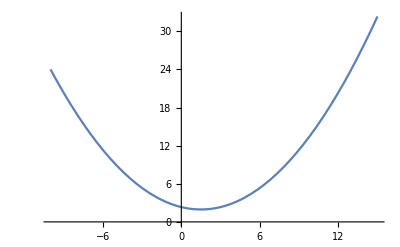

```mathematica
NMaximize[{x^2*Cos[x]+1,x>-3π/2&&x<3π},x]
```

{42.4032,{x→6.57833}}

```mathematica
NMinimize[{x^2*Cos[x]+1,x>-3π/2&&x<3π},x]
```

{-87.8264,{x→9.42478}}

```mathematica
h[x_]:=x^2*Cos[x]+1
```

```mathematica
h'[x]
```

2 x Cos[x]-x^2 Sin[x]

```mathematica
NSolve[h'[x]==0&&x>-3π/2&&x<3π,x]
```

{{x→-3.6436},{x→-1.07687},{x→0.},{x→1.07687},{x→3.6436},{x→6.57833}}

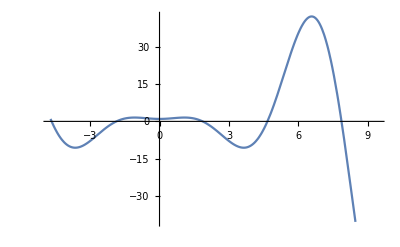

```mathematica
Plot[h[x],{x,-3π/2,3π}]
```

```mathematica
Newt[ff_,x_,eps_]:=Module[{x00=x},
While[Abs[ff[x00]]>eps,
x00=x00-ff[x00]/ff'[x00];];
x00
]
d[x_]:=Sin[x]-x^3-x^2+2x-1
```

```mathematica
Newt[d,1.0,10^-3]
```

0.926056

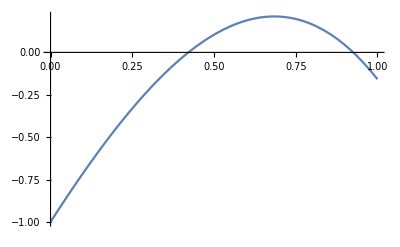

```mathematica
Plot[d[x],{x,0,1}]
```

```mathematica
Bisect[k_,epsilon_,xb_,xe_]:=Module[{xm, s0=xb,s1=xe},
While[Abs[k[s0]-k[s1]]>epsilon,
xm=(s0+s1)/2;
If[k[s0]*k[xm]>0,s0=xm,s1=xm]
]
N[s0]
]
```

```mathematica
Bisect[d,10^-2,0,1]
```

0.417969 Null